```mathematica
PlotEvolution[fn_]:=Module[{evol,numgen,size,avfitness,avfitnessplot,termfrac,termfracplot},

evol=ReadList[fn]; numgen=Length[evol]; size=evol[[1]]["Size"];
avfitness=Map[#["AvFitness"]&,evol];
termfrac=Map[#["NTerm"]&,evol]/size;
avfitnessplot=Show[ListLinePlot[avfitness,Frame->True,GridLines->Automatic,FrameLabel->{"generation","average fitness"}],ListPlot[avfitness,PlotStyle->Red],ImageSize->350];
termfracplot=Show[ListLinePlot[termfrac,Frame->True,GridLines->Automatic,FrameLabel->{"generation","terminal fraction"}],ListPlot[termfrac,PlotStyle->Red],ImageSize->350];

{avfitnessplot,termfracplot}];
```

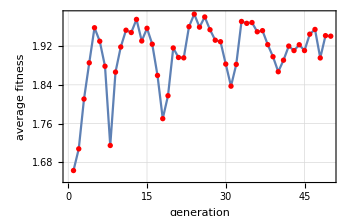
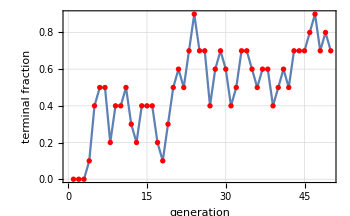

```mathematica
PlotEvolution[$HomeDirectory<>"/c/genetic/evol.m"]
```